# Harvest tree

Execute ALL the code cells first to complete function definitions. (execute any cell and choose Yes when you are asked if should automatically evaluate all the initialization cells)

blue cells should be execute one by one, red cells are for visualization only, they can be delete but not recommended . white cells are for debug only.

always note that the working coordinate system is graphic system NOT image system (flip the Y axis)

## Load street prediction from image

load the image, clean and binarize it

```mathematica
(*binarized image for the street detection*)
img=Binarize@Image@Import[NotebookDirectory[]<>"street.pdf"][[1]];
(*here a threshold that removes noise from the image, the rest, no matter whether they are really streets, are considered as streets*)
DeleteSmallComponents[img,15];
imgData=ImageData@img;
(*size of the input image*)
{m,n}=ImageDimensions@img;
```

random select a certain percentage of points from the image

```mathematica
SeedRandom[1];(*set random seed, for debug*)
ratio=0.1;
points={};
(*for each pixel of the image, if its white, it may be sampled*)
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
If[imgData[[j,i]]==1,
If[RandomReal[]<0.1,
AppendTo[points,{i,n-j}]
];
]
]
];
(*mapping from coordinate to index*)
pointsWithIndex=points[[#]]->#&/@Range@Length@points;
```

```mathematica
m
n
```

1057

1485

visualization of the random sampling

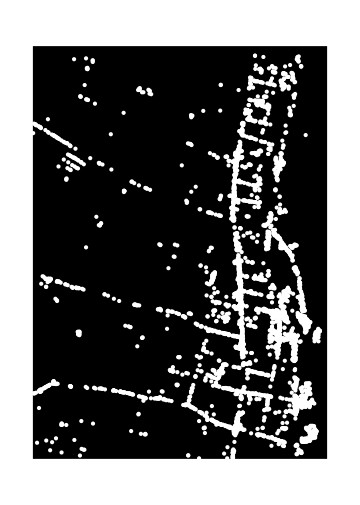

```mathematica
Graphics[{Black,Rectangle[{0,0},{m,n}],White,PointSize[Tiny],Point@points},ImageSize->Medium]
```

## Shortest path calculation

build a Delaunay mesh, convert it into edge-weighted graph for shortest distance calculation

use Delaunay mesh so that we don’t have to bother to extract a street network from the image, which makes the task much easier

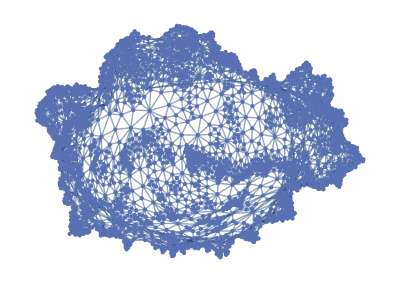

```mathematica
delaunay=DelaunayMesh@points;
(*elements of the mesh*)
nodes=MeshCells[delaunay,0];
edges=MeshCells[delaunay,1];
(*calculate the weights of the edges, currently use the squared euclidean distance, shorter edge gets higher priority*)
(*change the way of weight calculation to get better shortest path result*)
edgeWeights=N@SquaredEuclideanDistance[points[[#[[1,1]]]],points[[#[[1,2]]]]]&/@edges;
(*undirected edges for the graph*)
undirectedEdges=UndirectedEdge[#[[1,1]],#[[1,2]]]&/@edges;
(*undirected graph for shortest path calculation*)
g=Graph[undirectedEdges,EdgeWeight->edgeWeights]
```

just for validation

```mathematica
index=1;
edges[[index]]
edgeWeights[[index]]
edgeRules[[index]]
N@SquaredEuclideanDistance[points[[edges[[index,1,1]]]],points[[edges[[index,1,2]]]]]
```

Line[{92,85}]

793.

92<->85

793.

example: find shortest path between two points

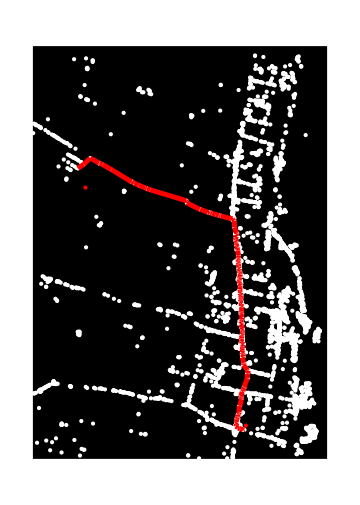

```mathematica
(*coordinate of two points, in graphic coordinate system NOT in Image coordinate system*)
p1={189,976};
p2={765,120};
(*index of closest points of p1 and p2*)
terminals=Flatten@Nearest[pointsWithIndex,{p1,p2}];
shortestPath=FindShortestPath[g,terminals[[1]],terminals[[2]]];
linesToDraw=Line[{points[[shortestPath[[#]]]], points[[shortestPath[[#+1]]]]}]&/@Range[Length@shortestPath-1];
Graphics[{Black,Rectangle[{0,0},{m,n}],PointSize[Tiny],White,Point@points,Red,Thickness[0.01],linesToDraw,Red,PointSize[Large],Point[{p1,p2}]},ImageSize->Medium]
```

## Load tree prediction from CSV

load the predicted trees

```mathematica
(*size of the corresponding image, ideally it should be the same size with street prediction, but just in case*)
w=17761;
h=25006;
(*number of type of trees*)
typeOfTrees=4;
(*import trees from a list of csv files*)
csvs={"eval_predict_paired.csv","eval_predict_rest.csv"};
(*here by default, the csv locates at the same directory with the notebook*)
trees=Flatten[Import[NotebookDirectory[]<>#,"CSV"]&/@csvs,1];
(*convert the coordinate system of trees from image to graphics, then adjust the coordinates to match the dimension of predicted streets*)
trees={N[#[[1]]/w * m], N[(1.0-#[[2]]/h)*n],#[[3]]}&/@trees;
(*transpose to select the 3rd channel, which represents the type of trees*)
treesT=Transpose@trees;
(*get the position (index) of each type of trees, note that the type starts from 0 not 1*)
indexOfEachType=Flatten@Position[treesT[[3]],#]&/@(Range[typeOfTrees]-1);
(*trees by types: a 2d array of [which type, which tree], the 3rd channel of trees are discarded*)
treesByType=trees[[#]][[1;;2]]&/@#&/@indexOfEachType;
(*all trees, in case of need*)
allTrees=Transpose@treesT[[1;;2]];
```

just for validation:

```mathematica
treesByType[[4,3]]
trees[[indexOfEachType[[4,3]]]]
```

{305.537,1346.04}

{305.537,1346.04,3}

show predicted trees

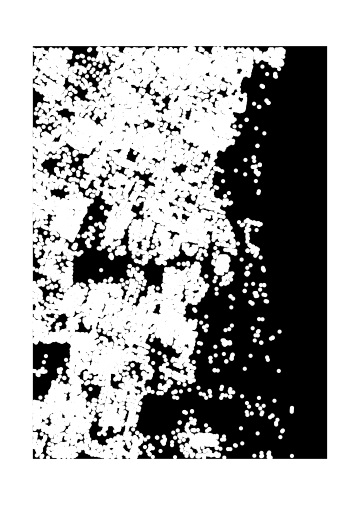

```mathematica
treesToShow=treesByType[[2]]; (*trees of interest, use allTrees or treesByType[[?]]*)
Graphics[{Black,Rectangle[{0,0},{m,n}],PointSize[Tiny],White,Point@treesToShow},ImageSize->Medium]
```

## Connect street data and tree data

select the type of tree

```mathematica
(*trees of interest, use allTrees or treesByType[[?]]*)
treesOfInterest=treesByType[[2]];
```

for each point of street, count the number of trees “belongs” to it

```mathematica
(*the nearest point for each tree*)
nearestPointsOfTrees=Flatten@Nearest[pointsWithIndex,treesOfInterest];
(*count the trees for each point*)
treeNumberPerPoint=ConstantArray[0,Length@points];
For[i=1,i≤Length@nearestPointsOfTrees,i++,
treeNumberPerPoint[[nearestPointsOfTrees[[i]]]]++;
]
```

visualize the mapping from trees to street points

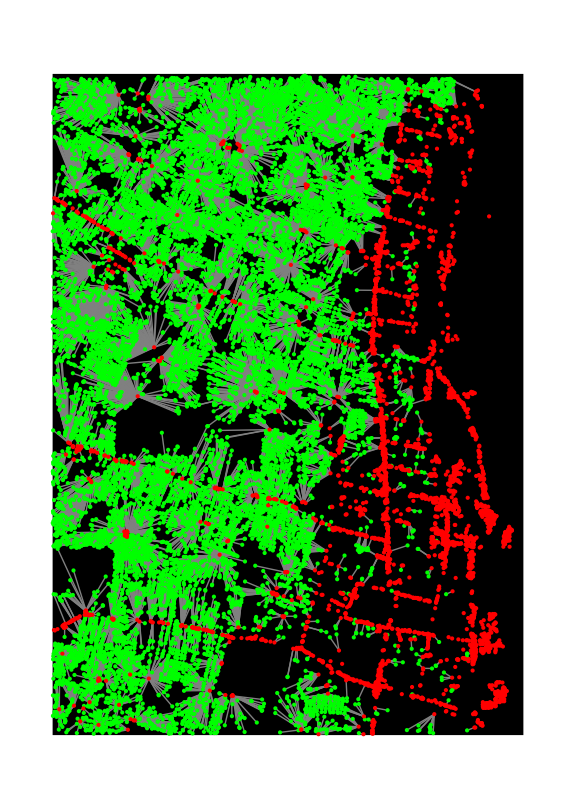

```mathematica
linesToDraw=Line[{points[[nearestPointsOfTrees[[#]]]],treesOfInterest[[#]]}]&/@Range@Length@treesOfInterest;
Graphics[{Black,Rectangle[{0,0},{m,n}],

Gray,Thickness[Tiny],linesToDraw,

PointSize[Tiny],Green,Point@treesOfInterest,

PointSize[Small],Red,Point@points

},
ImageSize->Large]
```

visualize the number of trees at each street point

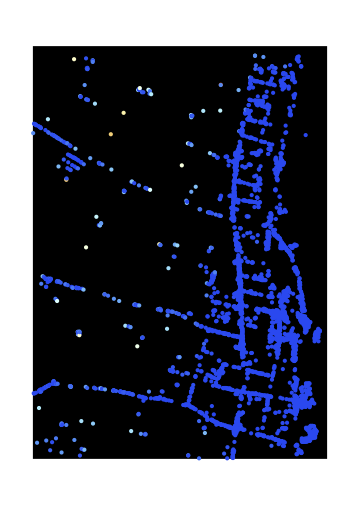

```mathematica
minMax=MinMax@treeNumberPerPoint;
scaledTreeNumPerPoint=N@Rescale[#,minMax]&/@treeNumberPerPoint;
pointsForVis=Table[{ColorData["LightTemperatureMap"][scaledTreeNumPerPoint[[i]]],Point[points[[i]]]},{i,1,Length@points}];
Graphics[{Black,Rectangle[{0,0},{m,n}],PointSize[Medium],pointsForVis},ImageSize->Medium]
```

example: find shortest path between points of interest and count how many trees there are in this path

2013 trees in the path with length of 2702.72 pixels

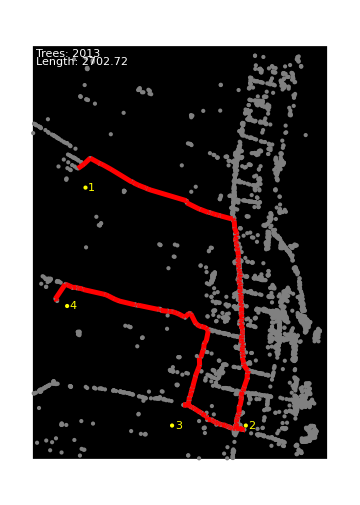

```mathematica
(*a list of points that wish to visit one follow the other*)
pointsOfInterests={{189,976},{765,120}, {500,120},{123,550}};

terminals=Flatten@Nearest[pointsWithIndex,pointsOfInterests];
(*join all the path and flatten it*)
shortestPath=Flatten[FindShortestPath[g,terminals[[#]],terminals[[#+1]]]&/@Range@(Length@pointsOfInterests-1),1];
(*remove duplicated nodes in the path, count the number of trees*)
numOfTreesInPath=Total[treeNumberPerPoint[[#]]&/@DeleteDuplicates[shortestPath]];
(*total length of the path, in pixel, scale them if exact meter is needed*)
lengthOfPath=N@EuclideanDistance[points[[shortestPath[[#]]]],points[[shortestPath[[#+1]]]]]&/@Range[Length@shortestPath-1];
lengthOfPath=Total[lengthOfPath];

Print[numOfTreesInPath, " trees in the path with length of ",lengthOfPath, " pixels"]

linesToDraw=Line[{points[[shortestPath[[#]]]], points[[shortestPath[[#+1]]]]}]&/@Range[Length@shortestPath-1];
Graphics[
{Black,Rectangle[{0,0},{m,n}],

PointSize[Tiny],Gray,Point@points,

Red,Thickness[0.01],linesToDraw,

Yellow,PointSize[Medium],Point@pointsOfInterests,

Text[#,pointsOfInterests[[#]]+{10,0},{-1,0}]&/@Range@Length@pointsOfInterests,

White, Text["Trees: "<> ToString@numOfTreesInPath , {10,n-10},{-1,1}],

Text["Length: " <> ToString@lengthOfPath, {10,n-40},{-1,1}]
},

ImageSize->Medium]
```

## Ask for best path by genetic algorithm

### genetic algorithm

```mathematica
(*
generate random gene (a set of points),

input: maxinum number of nodes (≥2), predefinded start and end point (or empty list if not applicable),

return: the gene
*)
RandomGene[maxNum_,startEnd_,width_,height_]:=
Module[{numOfPoints,points,immutable=(Length@startEnd==2)},
If[immutable,
numOfPoints=RandomInteger[{1,maxNum}],
numOfPoints=RandomInteger[{2,maxNum}]
];
points=RandomReal[{0,1},{numOfPoints,2}];
(*generate random points within the area*)
points=#*{width,height}&/@points;
(*if predefined endpoints exist, add them into the start and end of the list individually*)
If[immutable,
points=Insert[points,startEnd[[1]],1];
AppendTo[points,startEnd[[2]]];
];
(*at the begining, the fitness is set to negative infinity*)
Return@<|"points"->points,"endPointImmutable"->immutable,"fitness"->-Infinity|>;
];
```

```mathematica
(*produce the random cross over of two parent genes, the results are returned as new instance*)
Crossover[g1_, g2_]:=
(*note that the "=" in mathematica creates a copy of the original object, thus c1 and g1, c2 and g2 are different instances with the same value*)
Module[{c1=g1, c2=g2, len1=Length@g1["points"], len2=Length@g2["points"],p1, p2, list11,list12,list21,list22},
p1=RandomInteger[{1,len1-1}];
p2=RandomInteger[{1,len2-1}];

list11=c1["points"][[1;;p1]];
list12=c1["points"][[p1+1;;len1]];

list21=c2["points"][[1;;p2]];
list22=c2["points"][[p2+1;;len2]];

c1[["points"]]=Join[list11,list22];
c2[["points"]]=Join[list21,list12];

Return@{c1,c2};
];
```

```mathematica
(*given a set of point of interests and a graph object, calculate the shortest path pass the pois and the number of trees along this path*)
CountTreeAndPathLength[pointsOfInterests_,graphObj_]:=Module[
{graph=graphObj["graph"],points=graphObj["points"],
pointsWithIndex=graphObj["pointsWithIndex"],treeNumPerPoint=graphObj["treeNumPerPoint"],
terminals,shortestPath,numOfTreesInPath,lengthOfPath, distToTerminals},

terminals=Flatten@Nearest[pointsWithIndex,pointsOfInterests];
(*join all the path and flatten it*)
shortestPath=Flatten[FindShortestPath[graph,terminals[[#]],terminals[[#+1]]]&/@Range@(Length@pointsOfInterests-1),1];
(*remove duplicated nodes in the path, count the number of trees*)
numOfTreesInPath=Total[treeNumPerPoint[[#]]&/@DeleteDuplicates[shortestPath]];
(*total length of the path, in pixel, scale them if exact meter is needed*)
lengthOfPath=Total[N@EuclideanDistance[points[[shortestPath[[#]]]],points[[shortestPath[[#+1]]]]]&/@Range[Length@shortestPath-1]];
(*the distance between poi and terminals should also be counted*)
distToTerminals=Total[N@EuclideanDistance[pointsOfInterests[[#]],points[[terminals[[#]]]]]&/@Range@Length@pointsOfInterests];
Return@{numOfTreesInPath,lengthOfPath+distToTerminals};
]
```

fitness functions, all the functions have the same parameter structure: gene, param, graph
gene is the one that need to calculate its fitness
param is the necessary parameter for this fitness function
graph is the graph for shortest path calculation and tree counting

```mathematica
(*
calculate fitness, 

fitness = numTrees * w1 - length * w2,

Note: it is not good to access global variables from the inside of the function,
as function may be initialized before these variables and the code cannot run correctly,
thus, all the variables are put in the parameters, they are isolated with the function definition,

input: gene, street graph, street points, street point with index, tree num per street point,

return: the fitness
*)
FitnessTreeNumPathLength[gene_, wNum_,wLen_,graph_,points_,pointsWithIndex_,treeNumPerPoint_]:=
Module[{pointsOfInterests=gene["points"],terminals,shortestPath,numOfTreesInPath,lengthOfPath, distToTerminals},
terminals=Flatten@Nearest[pointsWithIndex,pointsOfInterests];
(*join all the path and flatten it*)
shortestPath=Flatten[FindShortestPath[graph,terminals[[#]],terminals[[#+1]]]&/@Range@(Length@pointsOfInterests-1),1];
(*remove duplicated nodes in the path, count the number of trees*)
numOfTreesInPath=Total[treeNumPerPoint[[#]]&/@DeleteDuplicates[shortestPath]];
(*total length of the path, in pixel, scale them if exact meter is needed*)
lengthOfPath=Total[N@EuclideanDistance[points[[#]],points[[#+1]]]&/@Range[Length@shortestPath-1]];
(*the distance between poi and terminals should also be counted*)
distToTerminals=Total[N@EuclideanDistance[pointsOfInterests[[#]],terminals[[#]]]&/@Range@Length@pointsOfInterests];
Return[wNum*numOfTreesInPath-wLen*(lengthOfPath+distToTerminals)];
];
```

```mathematica
(*x tree num, y length*)
Plot3D[x/Max[1,Power[(y/100),3]],{x,0,1000},{y,0,400}]
```

-Graphics3D-

```mathematica
(*
calculate fitness according to tree number, when the travel distance less than a upper bound,

param should contains: <|"maxLen"->Integer, "power"->Integer/Float|>,

the formula is: fitness = treeNum / (Max(1, Power(len / maxLen),power)),

the fitness gets lower once the len > maxLen, power controls how fast the fitness decrease
*)
FitnessByTreeNum[gene_,param_,graphObj_]:=
Module[{treeNum,pathLen, ratio},
{treeNum,pathLen}=CountTreeAndPathLength[gene["points"],graphObj];
(*ratio goes from 1 to Infinity*)
ratio=Max[1, Power[pathLen / param["maxLen"],param["power"]]];
Return[treeNum / ratio];
]
```

```mathematica
(*x length, y tree num*)
Plot3D[1/(1+x)*Min[1,Power[(y/100),3]],{x,0,1000},{y,0,200}]
```

-Graphics3D-

```mathematica
(*
calculate fitness according path length, when the tree number larger than a lower bound,

param should contains: <|"minNum"->Integer, "power"->Integer/Float|>,

the formula is: fitness = 1/(len+1) * (Min(1, Power(num / minNum),power)),

the fitness gets lower once the len > maxLen, power controls how fast the fitness decrease
*)
FitnessByPathLength[gene_,param_,graphObj_]:=
Module[{treeNum,pathLen, ratio},
{treeNum,pathLen}=CountTreeAndPathLength[gene["points"],graphObj];
ratio=Min[1,Power[treeNum/param["minNum"],param["power"]]];
Return[1/(1+pathLen)*ratio];
]
```

```mathematica
(*
mutate a gene, by randomly move some of its points, randomly swap some of its points, and randomly add/delete some of its points,

note that if endPointImmutable==true, then the start and end points will not be affected,

input: 
the gene, 
maximum/{minimum, maximum} move step, 
dimension ({width, height}) of the area, 
rate of a point be randomly moved, 
rate of randomly select two points and swap them, 
rate of randomly insert/delete a random point,

return: the mutated points of gene
*)
Mutate[gene_,moveStep_,dimension_,rateMovePoint_,rateSwapPoint_,rateInsertDelete_]:=
Module[{points=gene["points"],i, start=1,end,vec, id1, id2,tmp},
end=Length@points;
(*change the boundary so that end points are not affected*)
If[gene["endPointImmutable"],
start++;end--;
];
(*move mutation*)
For[i=start,i≤end,i++,
If[RandomReal[]<rateMovePoint, 
(*vector with random direction and random length*)
vec= RandomReal[moveStep]*N@Normalize@RandomReal[{-1,1},{2}] ;
points[[i]]+=vec;
]
];

(*swap mutation*)
While[RandomReal[]<rateSwapPoint,
id1=RandomInteger[{start,end}];
id2=RandomInteger[{start,end}];
If[id1≠id2,
tmp=points[[id1]];
points[[id1]]=points[[id2]];
points[[id2]]=tmp;
]
];

(*add/delete mutation*)
If[RandomReal[]<rateInsertDelete,
If[RandomReal[]<0.5,
(*remove one point, if there are extra points can be removed*)
If[end>start&&Length@points>3,
tmp=RandomInteger[{start,end}];
points=Delete[points,tmp]
],
(*else, insert one point*)
tmp=RandomInteger[{start,end+1}];
vec=RandomReal[dimension,{2}];
points=Insert[points,vec,tmp];
]
];

Return@points;
];
```

```mathematica
(*
wheel selection of num items based on val list, return the index of the items,
val must be positive!!!
*)
WheelSelection[val_,num_]:=
Module[{sum=Total@val,len=Length@val,key,count,list={},i},
While[Length@list<num,
key=RandomReal[sum];
count=0;
For[i=1,i≤len,i++,
count+=val[[i]];
If[count≥key,
AppendTo[list,i];
Break[];
]
]
];
Return@list;
];
```

```mathematica
WheelSelection[{1,2,3,4,5,6,7,8,9},3]
```

{9,3,7}

use genetic algorithm to optimize the path
input parameters see below.

Note that for fitness function, an association <|”function”-> XXX, “param”-><|XXX|>|> should be given. for what function param are, see FitnessByPathLength and FitnessByTreeNum

```mathematica
GeneticPathOptimization[metaParam_,geneParam_,mutationParam_,fitnessFunction_,graphObj_]:=
Module[
{curGenes,newGenes,iter=metaParam["iter"],population=metaParam["population"],fitness,selection,i,j,maxFitness=-Infinity},
(*random generate genes*)
curGenes=Table[RandomGene[geneParam["maxNumOfPoints"],geneParam["startEnd"],geneParam["width"],geneParam["height"]],{population}];
Monitor[
For[i=1,i<=iter,i++,
newGenes={};
(*calculate the fitness*)
fitness=fitnessFunction[["function"]][#,fitnessFunction["param"],graphObj]&/@curGenes;

(*Print@"s";*)
(*first round selection, remove those with low fitness*)
selection=WheelSelection[fitness,population];
fitness=fitness[[#]]&/@selection;
curGenes=curGenes[[#]]&/@selection;
maxFitness=Max[fitness];

(*Print@"c";*)
(*crossover*)
For[j=1,j<=population/2,j++,
(*need crossover?*)
If[RandomReal[]<metaParam["rateCrossover"],
(*randomly select two instances*)
selection=curGenes[[#]]&/@WheelSelection[fitness,2];
newGenes=Join[newGenes,Crossover[selection[[1]],selection[[2]]]];
]
];
(*if there are not enough new genes, select from old genes, make population to full*)
If[Length@newGenes<population,
selection=curGenes[[#]]&/@WheelSelection[fitness,population-Length@newGenes];
newGenes=Join[newGenes,selection];
];

(*Print@"m";*)
(*mutation*)
For[j=1,j<=population,j++,
newGenes[[j]][["points"]]=
Mutate[newGenes[[j]],
mutationParam["moveStep"],{geneParam["width"],geneParam["height"]},
mutationParam["rateMovePoint"],mutationParam["rateSwapPoint"],mutationParam["rateInsertDelete"]
];
];

(*assign new genes to cur genes*)
curGenes=newGenes;
],
{ProgressIndicator[i,{1,iter}],"best "<>ToString@maxFitness}
];
(*get latest fitness*)
fitness=fitnessFunction[["function"]][#,fitnessFunction["param"],graphObj]&/@curGenes;
(*sort the genes based on their fitness*)
For[j=1,j<=population,j++,
curGenes[[j]][["fitness"]]=fitness[[j]];
];
Return@SortBy[curGenes,-#["fitness"]&];
];
```

### ask path by GA

parameters for the optimization

```mathematica
(*where the path starts and ends, or empty list if not applicable*)
startEnd={{765,120},{765,120}};

(*fitness function to maximize tree num by setting upper bound of path length*)
fitnessTreeNum=<|"function"->FitnessByTreeNum,"param"-><|"maxLen"->2000,"power"->3|>|>;

(*fitness function to minimize travel distance by setting lower bound of tree number *)
fitnessPathLength=<|"function"->FitnessByPathLength,"param"-><|"minNum"->3000,"power"->3|>|>;

(*the graph for shortest path calculation*)
graphObj=<|"graph"->g,"points"->points,"pointsWithIndex"->pointsWithIndex,"treeNumPerPoint"-> treeNumberPerPoint|>;
(*mutation parameter, maximum move step of points, rate of move points, rate of swap points, rate of add/delete points*)
mutationParam=<|"moveStep"->100,"rateMovePoint"->0.3,"rateSwapPoint"->0.02,"rateInsertDelete"->0.02|>;
(*gene parameter, max num of points when generating a path, start-end points, dimensions*)
geneParam=<|"maxNumOfPoints"->5,"startEnd"->startEnd,"width"->m,"height"->n|>;
(*mate parameter, population, iteration, crossover rate*)
metaParam=<|"population"->200,"iter"->20,"rateCrossover"->0.5|>;
```

start the optimization process
change the fitness function to ask path differently

```mathematica
(*optimize the path, sort them from best to worst*)
genes=GeneticPathOptimization[metaParam,geneParam,mutationParam,fitnessTreeNum,graphObj];
```

visualize the results

this code needs to run once only

```mathematica
ShowPath[gene_]:=
Module[{pointsOfInterests=gene["points"],terminals,shortestPath,numOfTreesInPath,lengthOfPath,linesToDraw,distToTerminals},
terminals=Flatten@Nearest[pointsWithIndex,pointsOfInterests];
(*join all the path and flatten it*)
shortestPath=Flatten[FindShortestPath[g,terminals[[#]],terminals[[#+1]]]&/@Range@(Length@pointsOfInterests-1),1];
(*remove duplicated nodes in the path, count the number of trees*)
numOfTreesInPath=Total[treeNumberPerPoint[[#]]&/@DeleteDuplicates[shortestPath]];(*total length of the path, in pixel, scale them if exact meter is needed*)
lengthOfPath=Total[N@EuclideanDistance[points[[shortestPath[[#]]]],points[[shortestPath[[#+1]]]]]&/@Range[Length@shortestPath-1]];
distToTerminals=Total[N@EuclideanDistance[pointsOfInterests[[#]],points[[terminals[[#]]]]]&/@Range@Length@pointsOfInterests];
lengthOfPath+=distToTerminals;
linesToDraw=Line[{points[[shortestPath[[#]]]], points[[shortestPath[[#+1]]]]}]&/@Range[Length@shortestPath-1];
Return@Graphics[
{Black,Rectangle[{0,0},{m,n}],

PointSize[Tiny],Gray,Point@points,

Red,Thickness[0.01],linesToDraw,

Yellow,PointSize[Medium],Point@pointsOfInterests,

Text[#,pointsOfInterests[[#]]+{10,0},{-1,0}]&/@Range@Length@pointsOfInterests,

White, Text["Trees: "<> ToString@numOfTreesInPath , {10,n-10},{-1,1}],

Text["Length: " <> ToString@lengthOfPath, {10,n-50},{-1,1}],

Text["Fitness: "<> ToString@gene["fitness"] , {10,n-90},{-1,1}]
},

ImageSize->Medium]
];
```

run this to visualize

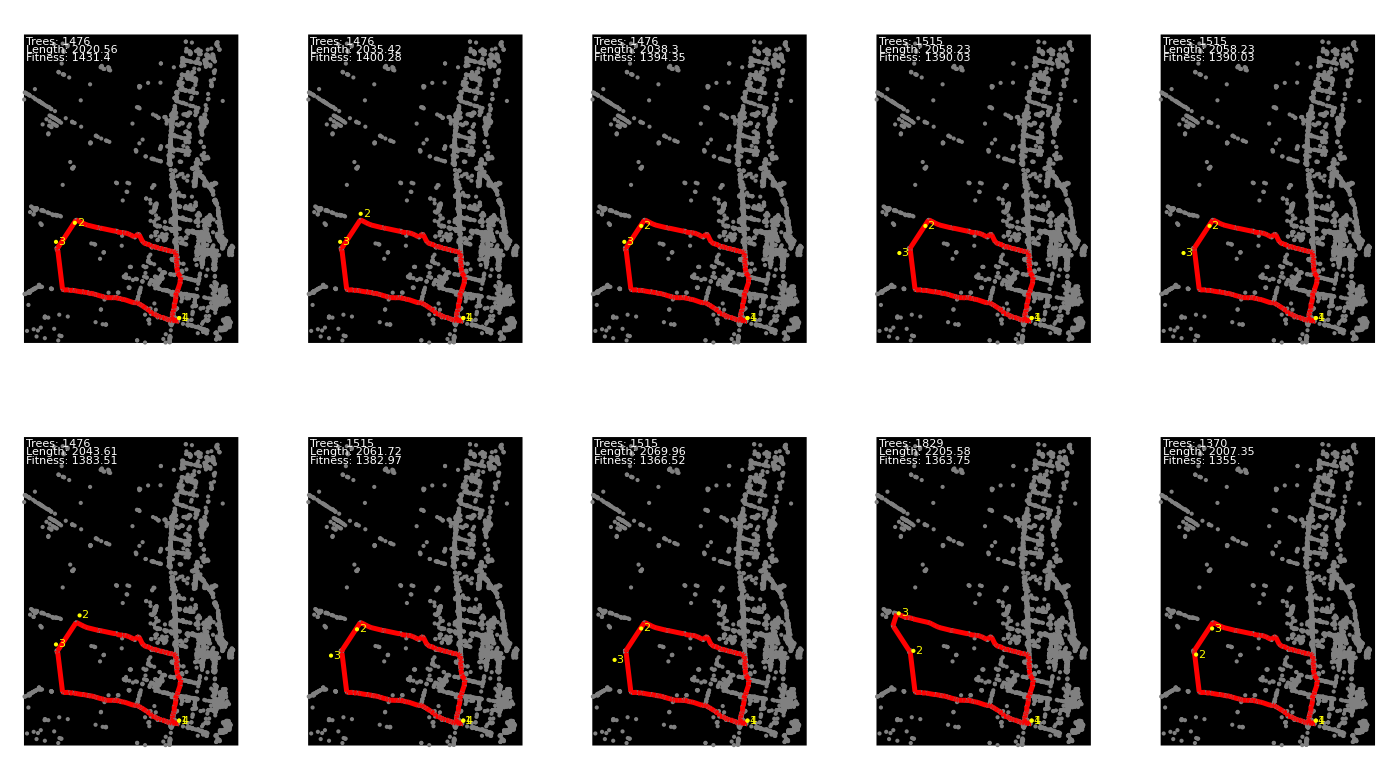

```mathematica
graphics=ShowPath[#]&/@genes[[1;;10]];
GraphicsGrid[Partition[graphics,5]]
```

```mathematica
(*population*)
population=2;
(*maxinum num of points in each path at the begining*)
maxNumOfPoints = 5;
(*predefined start and end points of the path (they are immutable during the optimization), or empty list if not applicable*)
startEnd={{0,0},{100,100}};
(*the random generated genes*)
genes=Table[RandomGene[maxNumOfPoints,startEnd,m,n],{population}];
```

```mathematica
genes
```

{<|points→{{0,0},{963.727,333.412},{68.9481,1160.9},{1042.29,327.951},{389.449,418.143},{100,100}},endPointImmutable→True,fitness→-∞|>,<|points→{{0,0},{974.063,1123.22},{796.523,693.184},{100,100}},endPointImmutable→True,fitness→-∞|>}

```mathematica
Crossover[genes[[1]],genes[[2]]]
```

{<|points→{{789.805,399.289},{814.972,182.372},{218.35,600.824},{858.559,811.72},{895.054,979.552},{116.451,1242.95}},endPointImmutable→False,fitness→0|>,<|points→{{190.905,1049.04},{669.614,1340.97},{291.467,631.27}},endPointImmutable→False,fitness→0|>}

```mathematica
FitnessTreeNumPathLength[genes[[1]],1,0.1,g,points,pointsWithIndex,treeNumberPerPoint]
FitnessTreeNumPathLength[genes[[2]],1,0.1,g,points,pointsWithIndex,treeNumberPerPoint]
```

-21605.

-7264.74

test of  move/swap/add-delete mutations

```mathematica
Mutate[genes[[1]],{10,100},{m,n},0.0,0.0,0.9]
```

{{0,0},{68.9481,1160.9},{1042.29,327.951},{389.449,418.143},{100,100}}

```mathematica
Mutate[genes[[1]],{10,100},{m,n},0.0,0.9,0.0]
```

{{0,0},{1042.29,327.951},{68.9481,1160.9},{963.727,333.412},{389.449,418.143},{100,100}}

```mathematica
Mutate[genes[[1]],{10,100},{m,n},0.9,0.0,0.0]
```

{{0,0},{897.77,318.435},{144.874,1204.01},{1009.16,356.926},{409.875,397.82},{100,100}}